# Patterns

The book

## Mathematica for students

1. 
Define a function f with a single argument. The function will return unevaluated unless
a. the argument is an even integer greater than 10. In this case the function returns the string “success”.
b. the argument is either an even integer, or is greater than 10. In this case the function returns the string “success”.

```mathematica
Clear[fA]
fA[x_Integer?(EvenQ[#]&&#>10 &)]:=Return["Success"]
fA /@ {9, -5,a, "s",3.5, 8,12, 12.5} 
fB[x_? ((EvenQ[#]&&IntegerQ[#])|| #>10 &)     ]:=Return["Success"]
fB /@ {9, -5,a, "s",3.5, 8,12, 12.5}
```

{fA[9],fA[-5],fA[a],fA[s],fA[3.5],fA[8],Success,fA[12.5]}

{fB[9],fB[-5],fB[a],fB[s],fB[3.5],Success,Success,Success}

3. 
Find a word that contains the five letters “angle,” (contiguous, and in that order) and which begins with the letter “q” and ends with the letter “s.”

```mathematica
DictionaryLookup["q"~~___~~"ang"~~___~~"s"]
DictionaryLookup[ RegularExpression["q.+ang.+s"]]
```

{quadrangles,quangos}

{quadrangles,quangos}

4. 
A DNA molecule is comprised of two complementary strands twisted into a double helix, where each strand may be represented as an ordered sequence of the letters A, C, G, and T. 

The complementary strand is built from a given strand by replacing every A by T, every T by A, every G by C, and every C by G. In other words, A is swapped with T, and C is swapped with G. 

Define a command complementaryDNA that will take a list of character strings from the four-letter alphabet “A”,”C”,”G”, and “T” (which is how we will represent a strand of DNA) and return the complementary strand, in which all As and Ts are switched, and in which all Gs and Cs are switched.

```mathematica
s={"A","G","T","C"};
replaceLetter[x_String]:=Piecewise[{{"A", x=="T"}, {"T", x=="A"}, {"G", x=="C"}, {"C", x=="G"}}];
complementaryDNA1[xx_List]:=replaceLetter /@ xx;
complementaryDNA1[s]

complementaryDNA2[xx_List]:=ReplaceAll[xx,{"A"-> "T", "T"->"A","G"->"C","C"->"G"}]
complementaryDNA2[s]
```

{T,C,A,G}

{T,C,A,G}

5. 
This exercise concerns the Collatz conjecture.

a. Write a command collatz, that when given a positive integer will return the orbit of that integer under the iterated Collatz process. The conjecture states that every orbit ends at 1, so use NestWhileList with iterations occurring as long as the iterated function does not return 1.
To be safe, put a cap on it so that it will never carry out more than 1000 iterations.

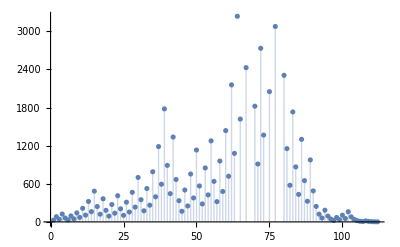

```mathematica
collatz[n_?EvenQ]:=n/2
collatz[n_?OddQ]:=3n+1
orbit[n_Integer]:=NestWhileList[collatz,n,(#>1)&,1,1000]
ListPlot[#,Filling->Bottom]&@   orbit@ 27
```

b. Run the collatz command on each of the first 20 integers, and make a Table of the results.
Map the command Length over this table to see how many iterations were carried out for each input. Make a ListPlot of the results. Did any number require all 1000 possible itera- tions? If not, we can be confident that every orbit ends in 1.

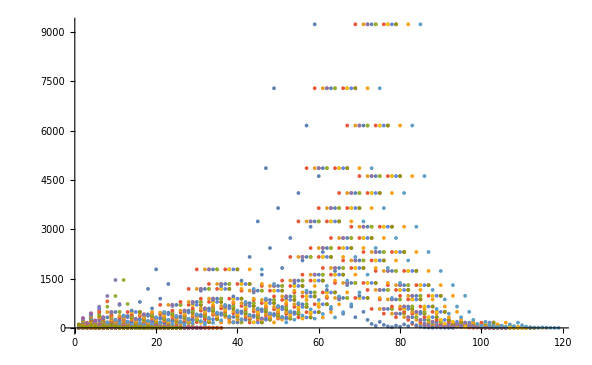

```mathematica
results=Table[orbit[i],{i,100}];
ListPlot[results,Filling->None,PlotRange-> Full]
```